## Импорт библиотек

```mathematica
If[$FrontEnd =!= Null, AppendTo[$Path, FileNameJoin[{NotebookDirectory[], #}]]&/@{"../../lib/mathematica","../lib"}];

(Once@Get[#] &) /@ { "Formal.m", "Features.m", "Ricci_grav.m", "Parameters.m", "Cache.m","aux-2-grav-generic.m" };
```

SetDelayed::write: Tag Div in Div[V_] is Protected.

```mathematica
EnableFeature[{Formatter[DD],Formatter[Tensor]}];
```

```mathematica
Quiet@CreateDirectory[FileNameJoin[{NotebookDirectory[], "dist"}]];
$cacheDir=FileNameJoin[{NotebookDirectory[], "cache"}];
RestoreCache[];
```

## Определения

### Система координат

```mathematica
Spher;
RecalculateGrav[];
```

### Базовые определения

#### Константы

```mathematica
l1=l(l+1)/2;
l2=(l-1)(l+2);
l3=l1 l2 / 2;
```

```mathematica
sql2=√l2;
```

#### Тензоры

```mathematica
thmask[Odd]=<|12->0,Even->0,Odd->0,13->1,23->1|>;
thmask[Even]=<|12->1,Even->1,Odd->1,13->0,23->0|>;

thmasked[m_][th_Association]:=th thmask[m];

metr={{1/r,1,Sin[u]},{1,r ,r Sin[u]},{Sin[u],r Sin[u],r Sin[u]^2}};

tha=<|KeyValueMap[(#1->(f[#1])#2)&,<|
12->LegendreP[l,1,Cos[u]],
Even->LegendreP[l,Cos[u]],
Odd->LegendreP[l,2,Cos[u]],
13->LegendreP[l,1,Cos[u]],
23->LegendreP[l,2,Cos[u]]
|>]|>;

MakeTensor[th_Association]:=metr{{-2th[Even],th[12],th[13]},{th[12],th[Even]+th[Odd],th[23]},{th[13],th[23],th[Even]-th[Odd]}};
MakeTensor[m_][th_Association]:=MakeTensor[th//thmasked[m]];
```

#### Решения

```mathematica
AllCached[
sln[f[11]]=-2sln[f[Even]],
sln[f[13]]=(l-1)(l+2)SphericalHankelH1[l,r ω],
sln[f[23]]=-(-2 f[r]-r f'[r])/((-1+l) (2+l))/.{f->(sln[f[13]]/.r->#&)}//FullSimplify,
sln[f[Even]]=(l(l+1))/2 sln[f[13]]/r/.{C[1]->C[3],C[2]->C[4]},
sln[f[Odd]]=-((4+l+l^2-2 r^2 ω^2) f[r]+2 r f'[r])/((-1+l) l (1+l) (2+l))/.{f->(sln[f[Even]]/.r->#&)}//FullSimplify,
sln[f[12]]=-(4 f[r]+2 r f'[r])/(l+l^2)/.{f->(sln[f[Even]]/.r->#&)}//FullSimplify
];
```

```mathematica
sln[eo:Even|Odd|All]:=Evaluate@(thmasked[eo][tha])/.{x:f[__]:>sln[x]};
```

#### Операторы повышения и понижения

```mathematica
up[Scalar,sgn_:+1][f_,m_]:=sgn I Exp[I sgn w](D[f,u]- m sgn Cot[u]f);
up[Vector,sgn_:+1][f_,m_]:=sgn I Exp[I sgn w](D[f,u]- m sgn Cot[u]f+sgn Csc[u]{{0,-I},{I,0}}.f );
up[Tensor,sgn_:+1][f_,m_]:=sgn I Exp[I sgn w](D[f,u]- m sgn Cot[u]f+2 sgn Csc[u]{{0,-I},{I,0}}.f);
```

```mathematica
up[All,sgn_:+1][th_,m_]:=Module[{thu=th},
thu[Even]=up[Scalar,sgn][#,m]&@th[Even];
{thu[12],thu[13]}=up[Vector,sgn][#,m]&@{th[12],th[13]};
{thu[23],thu[Odd]}=up[Tensor,sgn][#,m]&@{th[23],th[Odd]};
thu//Simplify
];
```

#### Функции

```mathematica
TensorNormRe[th_]:=Sum[hh[i,k]hh[j,l]ComplexExpand@Re[th[[i,j]]]ComplexExpand@Re[th[[k,l]]]//S,{i,3},{j,3},{k,3},{l,3}]//S;
```

```mathematica
Spher2Rect[expr_List]:=Spher2Rect/@(Transpose[{{Sin[u]Cos[w],Sin[u]Sin[w],Cos[u]},{Cos[u]Cos[w],Cos[u]Sin[w],-Sin[u]},{-Sin[w],Cos[w],0}}].expr);
```

```mathematica
Spher2Rect[expr_]:=expr/.{r->√(x^2+y^2+z^2),u->ArcTan[z,√(x^2+y^2)],w->ArcTan[x,y]}//S//PowerExpand//S;
```

```mathematica
SemiCurlCov[th0_]:=Module[{j},EvaluateAt[Table[(SSum[tm[i,j]TensorSr[th][j,k]/gd,j]//Tensorify//CovExpand)//.SSum2SumRules[{#,3}&]/.{TensorChristoffel[]:>cs2,TensorLeviCivita3[][a__]:>TensorLeviCivita3Value[a],tm[a__]:>Val[tm[a]]},{i,3},{k,3}]//ExpandAll,th[a__]:>th0[[a]]]]//Simplify;
```

#### Инварианты и соотношения

```mathematica
eq[sdivh][th_]:=Module[{i,j,k},Table[Sum[hh[j,k]ddd[th,i,j,k],{j,3},{k,3}],{i,3}]];
```

### Решатели и отображатели

#### Обобщенные табуляторы

```mathematica
series[eo__][{n_Integer}]:=Module[{l0},Table[series[eo][l0],{l0,2,n}]];
series[eo__][l0_Integer]:=Module[{m,s,sl},
Block[{l=l0},
s=sln[eo]//Normal//FunctionExpand//S//ComplexExpand//S//PowerExpand//S//Association;
sl={s};
Do[AppendTo[sl,s=(up[All][s,m-1]//Normal//S//ComplexExpand//S//PowerExpand//S//Association)],{m,1,l0}];
];
sl
];
```

```mathematica
intern[eo__][series][n_Integer,cfg_List:{energy,pointing,energy2,pointing2,TensorNormRe}]:=Module[{},
Cached[cache[eo][series]=series[eo][{n}],
Length[#]+1<n&];
Cached[cache[eo][series,Tensor]=ParallelTable[j Exp[-I ω ct]//MakeTensor[#]&,{i,cache[eo][series]},{j,i}],
Length[#]+1<n&];
If[MemberQ[cfg,energy],
Cached[cache[eo][series,energy]=
Table[EvaluateAt[epsnem,{th[a_,b_]:>j[[a,b]]}]//ComplexExpand//S,{i,cache[eo][series,Tensor][[1;;n-1]]},{j,i}],
Length[#//Evaluate]+1<n&
];
];
If[MemberQ[cfg,energy2],
Cached[cache[eo][series,energy2]=
Table[EvaluateAt[epscnem,{th[a_,b_]:>j[[a,b]]}]//ComplexExpand//S,{i,cache[eo][series,Tensor][[1;;n-1]]},{j,i}],
Length[#//Evaluate]+1<n&
];
];
If[MemberQ[cfg,pointing],
Cached[cache[eo][series,pointing]=
Table[EvaluateAt[Uinem,{th[a_,b_]:>j[[a,b]]}]//ComplexExpand//S,{i,cache[eo][series,Tensor][[1;;n-1]]},{j,i}],
Length[#//Evaluate]+1<n&
];
];
If[MemberQ[cfg,pointing2],
Cached[cache[eo][series,pointing2]=
Table[EvaluateAt[Uicnem,{th[a_,b_]:>j[[a,b]]}]//ComplexExpand//S,{i,cache[eo][series,Tensor][[1;;n-1]]},{j,i}],
Length[#//Evaluate]+1<n&
];
];
If[MemberQ[cfg,TensorNormRe],
Cached[cache[eo][series,TensorNormRe]=
Table[TensorNormRe[j],{i,cache[eo][series,Tensor][[1;;n-1]]},{j,i}],
Length[#//Evaluate]+1<n&
];
];
];
```

#### Плоттинг

```mathematica
splt[angle][f_,o:OptionsPattern[]]:=SphericalPlot3D[f/.{ω->1,ct->0},{u,0,π},{w,0,2π},o];
```

```mathematica
plt[radial][f_,range_,o:OptionsPattern[]]:=Plot[f,{r}~Join~range//Evaluate,o];
```

```mathematica
denplt[energy][f_,range_,o:OptionsPattern[]]:=Module[{f0=f/.{ω->1,ct->0,w->0}},
Module[{f1=(Spher2Rect@(f0//ComplexExpand//S))/.y->0},
DensityPlot[Abs[f1],{x}~Join~range//Evaluate,{z}~Join~range//Evaluate,o]//Quiet
]];
```

```mathematica
plt3d[energy][f_,range_,o:OptionsPattern[]]:=Module[{f0=f/.{ω->1,ct->0,w->0}},
Module[{f1=(Spher2Rect@(f0//ComplexExpand//S))/.y->0},
Plot3D[f1,{x}~Join~range//Evaluate,{z}~Join~range//Evaluate,o]//Quiet
]];
```

```mathematica
denplt[pointing,i_Integer][f_,range_,o:OptionsPattern[]]:=Module[{f0=f/.{ω->1,ct->0,w->0}},
Module[{f1=(Spher2Rect/@(f0//ComplexExpand//S))/.y->0},DensityPlot[Abs[(f1)[[i]]],{x}~Join~range//Evaluate,{z}~Join~range//Evaluate,o]//Quiet]];
```

```mathematica
denplt[pointing,i_List][f_,range_,o:OptionsPattern[]]:=denplt[pointing,#][f,range,o]&/@i;
```

```mathematica
plt3d[pointing,i_Integer][f_,range_,o:OptionsPattern[]]:=Module[{f0=f/.{ω->1,ct->0,w->0}},
Module[{f1=(Spher2Rect/@(f0//ComplexExpand//S))/.y->0},Plot3D[(f1)[[i]],{x}~Join~range//Evaluate,{z}~Join~range//Evaluate,o]//Quiet]];
```

```mathematica
plt3d[pointing,i_List][f_,range_,o:OptionsPattern[]]:=plt3d[pointing,#][f,range,o]&/@i;
```

```mathematica
vecplt[pointing,XOZ,yoff_:0][f_,range_,o:OptionsPattern[]]:=Module[{f0=f/.{ω->1,ct->0,w->0}},
Module[{f1=((Spher2Rect@(f0//ComplexExpand//S)))/.y->yoff},
StreamPlot[{f1[[1]],f1[[3]]},{x}~Join~range//Evaluate,{z}~Join~range//Evaluate,o,StreamPoints->Fine]//Quiet]];
```

```mathematica
vecplt[pointing,XOY,zoff_:0][f_,range_,o:OptionsPattern[]]:=Module[{f0=f/.{ω->1,ct->0,w->0}},
Module[{f1=((Spher2Rect@(f0//ComplexExpand//S)))/.z->zoff},
StreamPlot[{f1[[1]],f1[[2]]},{x}~Join~range//Evaluate,{y}~Join~range//Evaluate,o,StreamPoints->Fine]//Quiet]];
```

```mathematica
contplt[pointing,i_Integer][f_,range_,o:OptionsPattern[]]:=Module[{f0=f/.{ω->1,ct->0,w->0}},
Module[{f1=(Spher2Rect/@(f0//ComplexExpand//S))/.y->0},DensityPlot[(f1)[[i]],{x}~Join~range//Evaluate,{z}~Join~range//Evaluate,o]//Quiet]];
```

```mathematica
contplt[pointing,i_List][f_,range_,o:OptionsPattern[]]:=contplt[pointing,#][f,range,o]&/@i;
```

## Волны общего вида

### Угловые части

```mathematica
intern[Odd][series][5,{TensorNormRe}];
intern[Even][series][5,{TensorNormRe}];
```

```mathematica
InCache["Media",Cached[cache[Odd][angle,splt]=With[{lm={{1,1},{1,2},{1,3},{2,1},{2,2},{2,3},{2,4}}},
{({#[[1]]+1,#[[2]]-1}&)/@lm}~Join~Table[splt[angle][#, PlotRange->Full]&/@(cache[Odd][series,TensorNormRe][[Sequence@@#]]&/@lm)//Parallelize,{r,{0.1,2,4,6,10,100}}]]]
];
cache[Odd][angle,splt]//Grid//Rasterize
```

-Graphics-

```mathematica
InCache["Media",Cached[cache[Even][angle,splt]=With[{lm={{1,1},{1,2},{1,3},{2,1},{2,2},{2,3},{2,4}}},
{({#[[1]]+1,#[[2]]-1}&)/@lm}~Join~Table[splt[angle][#, PlotRange->Full]&/@(cache[Even][series,TensorNormRe][[Sequence@@#]]&/@lm)//Parallelize,{r,{0.1,2,4,6,10,100}}]]]
];
cache[Even][angle,splt]//Grid//Rasterize
```

-Graphics-

### Радиальные части

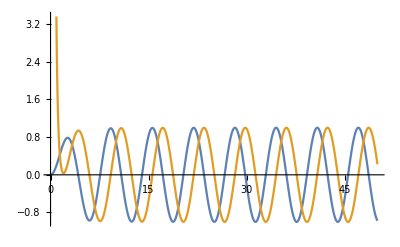
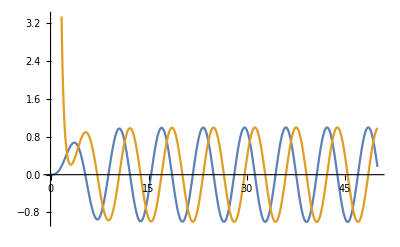
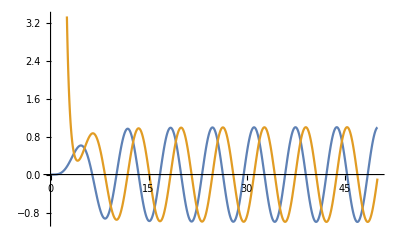
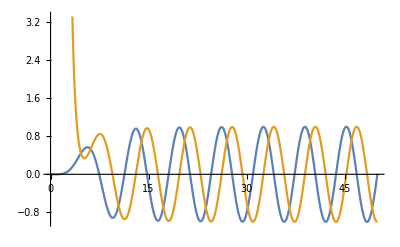
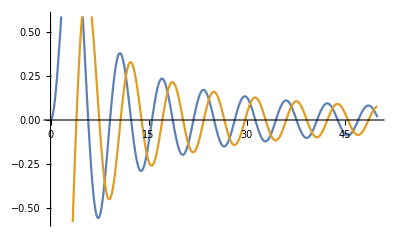
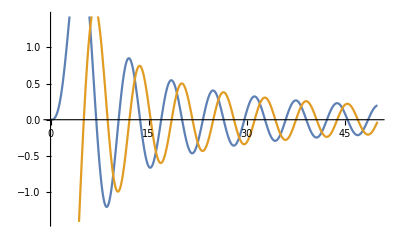
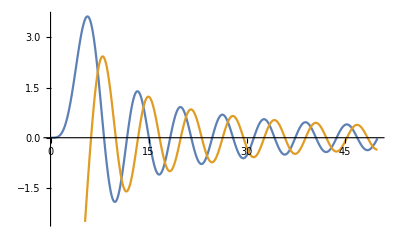
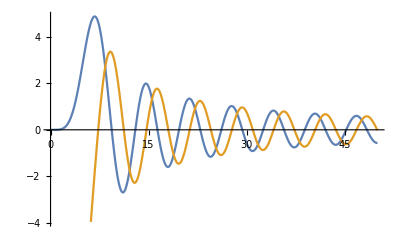
f23 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
f13 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
fe | -Graphics- | -Graphics- | -Graphics- | -Graphics-
fo | -Graphics- | -Graphics- | -Graphics- | -Graphics-
f12 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{
{"f23"}~Join~Table[plt[radial][sln[f[23]]/.{ω->1}//ReIm,{0,50}],{l,2,5}],
{"f13"}~Join~Table[plt[radial][sln[f[13]]/.{ω->1}//ReIm,{0,50}],{l,2,5}],
{"fe"}~Join~Table[plt[radial][sln[f[Even]]/.{ω->1}//ReIm,{0,50}],{l,2,5}],
{"fo"}~Join~Table[plt[radial][sln[f[Odd]]/.{ω->1}//ReIm,{0,50}],{l,2,5}],
{"f12"}~Join~Table[plt[radial][sln[f[12]]/.{ω->1}//ReIm,{0,50}],{l,2,5}]
},Frame->All]
```

### Плотность и поток энергии

#### Нечетные моды

```mathematica
intern[Odd][series][3];
```

```mathematica
cache[Odd][energy,plt3d]={plt3d[energy][#,{-10,10},MaxRecursion->0,PlotPoints->50]&/@(-cache[Odd][series,energy][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize};
%//Grid//Rasterize
```

-Graphics-

```mathematica
cache[Odd][energy,denplt]={denplt[energy][#,{-10,10},MaxRecursion->0,PlotPoints->100]&/@(-cache[Odd][series,energy][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize};
%//Grid//Rasterize
```

-Graphics-

```mathematica
cache[Odd][pointing,plt3d]={plt3d[pointing,{1,2,3}][#,{-10,10},MaxRecursion->0,PlotPoints->50]&/@(cache[Odd][series,pointing][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize//Transpose}//Flatten[#,1]&;
%//Grid//Rasterize
```

-Graphics-

```mathematica
cache[Odd][pointing,denplt]={denplt[pointing,{1,2,3}][#,{-10,10},MaxRecursion->0,PlotPoints->100]&/@(cache[Odd][series,pointing][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize//Transpose}//Flatten[#,1]&;
%//Grid//Rasterize
```

-Graphics-

```mathematica
cache[Odd][pointing,vecplt]={vecplt[pointing,XOZ,0][#,{-2,2},MaxRecursion->0]&/@(-cache[Odd][series,pointing][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize};
%//Grid//Rasterize
```

-Graphics-

#### Нечетные моды (lagrc2)

```mathematica
intern[Odd][series][3];
```

```mathematica
cache[Odd][energy2,plt3d]={plt3d[energy][#,{-10,10},MaxRecursion->0,PlotPoints->50]&/@(-cache[Odd][series,energy2][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize};
%//Grid//Rasterize
```

-Graphics-

```mathematica
cache[Odd][energy2,denplt]={denplt[energy][#,{-10,10},MaxRecursion->0,PlotPoints->100]&/@(-cache[Odd][series,energy2][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize};
%//Grid//Rasterize
```

-Graphics-

```mathematica
cache[Odd][pointing2,plt3d]={plt3d[pointing,{1,2,3}][#,{-10,10},MaxRecursion->0,PlotPoints->50]&/@(cache[Odd][series,pointing2][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize//Transpose}//Flatten[#,1]&;
%//Grid//Rasterize
```

-Graphics-

```mathematica
cache[Odd][pointing2,denplt]={denplt[pointing,{1,2,3}][#,{-10,10},MaxRecursion->0,PlotPoints->100]&/@(cache[Odd][series,pointing2][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize//Transpose}//Flatten[#,1]&;
%//Grid//Rasterize
```

-Graphics-

```mathematica
cache[Odd][pointing2,vecplt]={vecplt[pointing,XOY,0.001][#,{-2,2},MaxRecursion->0]&/@(-cache[Odd][series,pointing2][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize};
%//Grid//Rasterize
```

-Graphics-

#### Четные моды

```mathematica
intern[Even][series][3];
```

```mathematica
cache[Even][energy,plt3d]={plt3d[energy][#,{-10,10},MaxRecursion->0,PlotPoints->50]&/@(-cache[Even][series,energy][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize};
%//Grid//Rasterize
```

-Graphics-

```mathematica
cache[Even][energy,denplt]={denplt[energy][#,{-10,10},MaxRecursion->0,PlotPoints->100]&/@(-cache[Even][series,energy][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize};
%//Grid//Rasterize
```

-Graphics-

```mathematica
cache[Even][pointing,plt3d]={plt3d[pointing,{1,2,3}][#,{-10,10},MaxRecursion->0,PlotPoints->50]&/@(-cache[Even][series,pointing][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize//Transpose}//Flatten[#,1]&;
%//Grid//Rasterize
```

-Graphics-

```mathematica
cache[Even][pointing,denplt]={denplt[pointing,{1,2,3}][#,{-10,10},MaxRecursion->0,PlotPoints->100]&/@(-cache[Even][series,pointing][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize//Transpose}//Flatten[#,1]&;
%//Grid//Rasterize
```

-Graphics-

```mathematica
cache[Even][pointing,vecplt]={vecplt[pointing,XOZ,0][#,{-2,2},MaxRecursion->0]&/@(-cache[Even][series,pointing][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize};
%//Grid//Rasterize
```

-Graphics-

#### Четные моды (lagrc2)

```mathematica
intern[Even][series][3];
```

```mathematica
cache[Even][energy2,plt3d]={plt3d[energy][#,{-10,10},MaxRecursion->0,PlotPoints->50]&/@(-cache[Even][series,energy2][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize};
%//Grid//Rasterize
```

-Graphics-

```mathematica
cache[Even][energy2,denplt]={denplt[energy][#,{-10,10},MaxRecursion->0,PlotPoints->100]&/@(-cache[Even][series,energy2][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize};
%//Grid//Rasterize
```

-Graphics-

```mathematica
cache[Even][pointing2,plt3d]={plt3d[pointing,{1,2,3}][#,{-10,10},MaxRecursion->0,PlotPoints->50]&/@(-cache[Even][series,pointing2][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize//Transpose}//Flatten[#,1]&;
%//Grid//Rasterize
```

-Graphics-

```mathematica
cache[Even][pointing2,denplt]={denplt[pointing,{1,2,3}][#,{-10,10},MaxRecursion->0,PlotPoints->100]&/@(-cache[Even][series,pointing2][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize//Transpose}//Flatten[#,1]&;
%//Grid//Rasterize
```

-Graphics-

```mathematica
cache[Even][pointing2,vecplt]={vecplt[pointing,XOY,0.01][#,{-2,2},MaxRecursion->0]&/@(-cache[Even][series,pointing2][[Sequence@@#]]&/@{{1,1},{1,2},{2,1},{2,3}})//Parallelize};
%//Grid//Rasterize
```

-Graphics-

### Различные соотношения

#### Равенство нулю дивергенции

```mathematica
intern[Odd][series][5,{}]
```

```mathematica
eq[sdivh][cache[Odd][series,Tensor][[Sequence@@#]]]&/@{{1,1},{2,1},{3,1},{4,1}};
Table[%,{r,Range[3,5,0.66]}]/.{u->RandomReal[{0,π}],ω->1,ct->0}//Simplify//Chop
```

{{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}}}

```mathematica
eq[sdivh][cache[Odd][series,Tensor][[Sequence@@#]]]&/@{{1,2},{2,3}};
Table[%,{r,Range[3,5,0.66]}]/.{u->RandomReal[{0,π}],w->RandomReal[{0,2π}],ω->1,ct->0}//Simplify//Chop
```

{{{0,1.65879+0.572029 ⅈ,-1.11547+3.23466 ⅈ},{0,-2.32705-24.7437 ⅈ,47.3016-4.44853 ⅈ}},{{0,0.9941+1.14576 ⅈ,-2.23425+1.93851 ⅈ},{0,0.32983-24.4484 ⅈ,46.7369+0.630521 ⅈ}},{{0,0.189601+1.3077 ⅈ,-2.55003+0.369725 ⅈ},{0,8.71992-21.1483 ⅈ,40.4282+16.6695 ⅈ}},{{0,-0.508902+1.04815 ⅈ,-2.04391-0.992367 ⅈ},{0,15.9902-13.5386 ⅈ,25.8811+30.5678 ⅈ}}}

```mathematica
intern[Even][series][5,{}]
```

```mathematica
eq[sdivh][cache[Even][series,Tensor][[Sequence@@#]]]&/@{{1,1},{2,1},{3,1},{4,1}};
Table[%,{r,Range[3,5,0.66]}]/.{u->RandomReal[{0,π}],ω->1,ct->0}//Simplify//Chop
```

{{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}}}

```mathematica
eq[sdivh][cache[Even][series,Tensor][[Sequence@@#]]]&/@{{1,2},{2,3}};
Table[%,{r,Range[3,5,0.66]}]/.{u->RandomReal[{0,π}],w->RandomReal[{0,2π}],ω->1,ct->0}//Simplify//Chop
```

{{{0,3.21482+1.58946 ⅈ,-2.11496+4.27769 ⅈ},{0,6.79273+52.88 ⅈ,3.8999-0.500963 ⅈ}},{{0,1.64617+2.56465 ⅈ,-3.41256+2.19042 ⅈ},{0,-10.8655+47.3758 ⅈ,3.49396+0.80133 ⅈ}},{{0,-0.0143592+2.63539 ⅈ,-3.50669-0.0191065 ⅈ},{0,-26.7221+34.1821 ⅈ,2.52093+1.97075 ⅈ}},{{0,-1.31438+1.90671 ⅈ,-2.5371-1.74893 ⅈ},{0,-35.6276+15.5086 ⅈ,1.14376+2.62754 ⅈ}}}

#### Эквивалентность sr(odd)=even

```mathematica
cache[Odd][l->1,m->1,Re]=cache[Odd][series,Tensor][[1,1]]//Re//ComplexExpand//Simplify;
```

```mathematica
cache[Odd][sr]=SemiCurlCov[cache[Odd][l->1,m->1,Re]];
%//MatrixForm
```

(-(6 (1+3 Cos[2 u]) (-3 r ω Cos[(ct-r) ω]+(-3+r^2 ω^2) Sin[(ct-r) ω]))/(r^5 ω^3) | -(6 Sin[2 u] (r ω (-6+r^2 ω^2) Cos[(ct-r) ω]+3 (-2+r^2 ω^2) Sin[(ct-r) ω]))/(r^4 ω^3) | 0
-(6 Sin[2 u] (r ω (-6+r^2 ω^2) Cos[(ct-r) ω]+3 (-2+r^2 ω^2) Sin[(ct-r) ω]))/(r^4 ω^3) | (3 (4 Cos[u]^2 (-3 r ω Cos[(ct-r) ω]+(-3+r^2 ω^2) Sin[(ct-r) ω])+Sin[u]^2 ((9 r ω-2 r^3 ω^3) Cos[(ct-r) ω]+(9-5 r^2 ω^2+r^4 ω^4) Sin[(ct-r) ω])))/(r^3 ω^3) | 0
0 | 0 | (3 Sin[u]^2 (4 Cos[u]^2 (-3 r ω Cos[(ct-r) ω]+(-3+r^2 ω^2) Sin[(ct-r) ω])+Sin[u]^2 (r ω (3+2 r^2 ω^2) Cos[(ct-r) ω]+(3+r^2 ω^2-r^4 ω^4) Sin[(ct-r) ω])))/(r^3 ω^3))

```mathematica
cache[Even][l->1,m->1,Re]=cache[Even][series,Tensor][[1,1]]//Re//ComplexExpand//Simplify;
%//MatrixForm
```

(-(6 (1+3 Cos[2 u]) (-3 r ω Cos[(ct-r) ω]+(-3+r^2 ω^2) Sin[(ct-r) ω]))/(r^5 ω^3) | -(6 Sin[2 u] (r ω (-6+r^2 ω^2) Cos[(ct-r) ω]+3 (-2+r^2 ω^2) Sin[(ct-r) ω]))/(r^4 ω^3) | 0
-(6 Sin[2 u] (r ω (-6+r^2 ω^2) Cos[(ct-r) ω]+3 (-2+r^2 ω^2) Sin[(ct-r) ω]))/(r^4 ω^3) | -(3 (2 r ω (3+2 r^2 ω^2) Cos[(ct-r) ω]+(21 r ω-2 r^3 ω^3) Cos[2 u+ct ω-r ω]+21 r ω Cos[2 u-ct ω+r ω]-2 r^3 ω^3 Cos[2 u-ct ω+r ω]+6 Sin[(ct-r) ω]+2 r^2 ω^2 Sin[(ct-r) ω]-2 r^4 ω^4 Sin[(ct-r) ω]+21 Sin[2 u+ct ω-r ω]-9 r^2 ω^2 Sin[2 u+ct ω-r ω]+r^4 ω^4 Sin[2 u+ct ω-r ω]-21 Sin[2 u-ct ω+r ω]+9 r^2 ω^2 Sin[2 u-ct ω+r ω]-r^4 ω^4 Sin[2 u-ct ω+r ω]))/(4 r^3 ω^3) | 0
0 | 0 | -(3 Sin[u]^2 (-2 r ω (-9+2 r^2 ω^2) Cos[(ct-r) ω]+r ω (15+2 r^2 ω^2) Cos[2 u+ct ω-r ω]+15 r ω Cos[2 u-ct ω+r ω]+2 r^3 ω^3 Cos[2 u-ct ω+r ω]+18 Sin[(ct-r) ω]-10 r^2 ω^2 Sin[(ct-r) ω]+2 r^4 ω^4 Sin[(ct-r) ω]+15 Sin[2 u+ct ω-r ω]-3 r^2 ω^2 Sin[2 u+ct ω-r ω]-r^4 ω^4 Sin[2 u+ct ω-r ω]-15 Sin[2 u-ct ω+r ω]+3 r^2 ω^2 Sin[2 u-ct ω+r ω]+r^4 ω^4 Sin[2 u-ct ω+r ω]))/(4 r^3 ω^3))

```mathematica
cache[Odd][sr]-cache[Even][l->1,m->1,Re]//Simplify
```

{{0,0,0},{0,0,0},{0,0,0}}

#### Бироторное уравнение br h = o^2 h

```mathematica
cache[Odd][srsr]=SemiCurlCov[cache[Odd][sr]];
```

```mathematica
%//MatrixForm
```

(0 | 0 | -(12 Cos[u] Sin[u]^2 (-3 r ω Cos[(ct-r) ω]+(-3+r^2 ω^2) Sin[(ct-r) ω]))/(r^3 ω)
0 | 0 | -(3 Sin[u]^3 (r ω (-3+r^2 ω^2) Cos[(ct-r) ω]+(-3+2 r^2 ω^2) Sin[(ct-r) ω]))/(r^2 ω)
(6 Sin[u] Sin[2 u] (3 r ω Cos[(ct-r) ω]+(3-r^2 ω^2) Sin[(ct-r) ω]))/(r^3 ω) | -(3 Sin[u]^3 (r ω (-3+r^2 ω^2) Cos[(ct-r) ω]+(-3+2 r^2 ω^2) Sin[(ct-r) ω]))/(r^2 ω) | 0)

```mathematica
cache[Odd][srsr]-ω^2 cache[Odd][l->1,m->1,Re]//Simplify
```

{{0,0,0},{0,0,0},{0,0,0}}

### Отчет

#### Угловые части нечетных мод в ближней и дальней зоне

```mathematica
intern[Odd][series][4,{TensorNormRe}];
```

```mathematica
cache[Odd][angle,splt,report]=Module[{ll,mm},
Table[
ParallelTable[
With[{fn=cache[Odd][series,TensorNormRe][[ll,mm]]},
With[{maxfn=Max[Outer[((fn/.{u->#1,w->#2})//N)&,RandomReal[{0,π},5],RandomReal[{0,2π},5]]]},
splt[angle][fn/maxfn, PlotRange->Full,Boxed-> False,Axes-> False]
]
],{ll,1,3},{mm,1,ll+2}
]
,{r,{0.3,300}}]
];
```

```mathematica
cache[Odd][angle,splt,report, Image]=With[{modes=cache[Odd][angle,splt,report], styled=Style[#,FontSize->Large]&},
With[{tbl=Table[Prepend[#[[ll]],styled@StringForm["l = ``",ll+1]],{ll,1,3}]&/@modes},
With[{res={""}~Join~Table[styled@StringForm["m = ``",m],{m,0,4}]},
Rasterize[Grid[Prepend[#,res]],ImageResolution->100]&/@tbl
]
]
];
%//Column
```

-Graphics-
-Graphics-

```mathematica
Quiet@CreateDirectory[FileNameJoin[{NotebookDirectory[], "dist"}]];
Export[FileNameJoin[{NotebookDirectory[], "dist", #[[1]]}],#[[2]]]&/@(Inner[{#1,#2}&,{"angle-modes-odd-near.png", "angle-modes-odd-far.png"},cache[Odd][angle,splt,report, Image],List]);
```

#### Плотность и поток энергии нечетных мод

```mathematica
intern[Odd][series][3];
```

```mathematica
cache[Odd][energy,plt3d,report]={plt3d[energy][#,{-10,10},MaxRecursion->0,PlotPoints->50,AxesLabel->{"x","z","ϵ"}]&/@(-cache[Odd][series,energy][[Sequence@@#]]&/@{{1,1},{1,3},{2,1},{2,4}})//Parallelize};
```

```mathematica
cache[Odd][energy,denplt,report]={denplt[energy][#,{-10,10},MaxRecursion->0,PlotPoints->50,FrameLabel->{"x","z"}]&/@(-cache[Odd][series,energy][[Sequence@@#]]&/@{{1,1},{1,3},{2,1},{2,4}})//Parallelize};
```

```mathematica
cache[Odd][energy,plt3d,report,Image]=With[{styled=Style[#,FontSize->Large]&},
With[{labels=styled/@{"ϵ_20","ϵ_22","ϵ_30","ϵ_33"}},
Rasterize[Grid[({labels}~Join~cache[Odd][energy,plt3d,report]~Join~cache[Odd][energy,denplt,report])],ImageResolution->100]
]
]
```

-Graphics-

```mathematica
cache[Odd][pointing,plt3d,report]={plt3d[pointing,{1,2}][#,{-5,5},MaxRecursion->0,PlotPoints->100,AxesLabel->{"x","z","U^i"}]&/@(cache[Odd][series,pointing][[Sequence@@#]]&/@{{1,1},{2,1}})//Parallelize//Transpose}//Flatten[#,2]&;
```

```mathematica
cache[Odd][pointing,denplt,report]={contplt[pointing,{1,2}][#,{-5,5},MaxRecursion->0,PlotPoints->100,FrameLabel->{"x","z"}]&/@(cache[Odd][series,pointing][[Sequence@@#]]&/@{{1,1},{2,1}})//Parallelize//Transpose}//Flatten[#,2]&;
```

```mathematica
cache[Odd][pointing,report,Image]=With[{styled=Style[#,FontSize->Large]&},With[{labels=styled/@{"U_20^r","U_20^θ","U_30^r","U_30^θ"}},
Rasterize[Grid[{labels,cache[Odd][pointing,plt3d,report],cache[Odd][pointing,denplt,report]}],ImageResolution->100]
]
]
```

-Graphics-

```mathematica
cache[Odd][pointing,vecplt,report]={Pane@vecplt[pointing][#,{-2.5,2.5},MaxRecursion->0,FrameLabel->{"x","z"}]&/@(-cache[Odd][series,pointing][[Sequence@@#]]&/@{{1,1},{2,1}})//Parallelize};
```

```mathematica
cache[Odd][pointing,vecplt,report,Image]=With[{labels={"U_20","U_30"}},
Rasterize[Grid[cache[Odd][pointing,vecplt,report]],ImageResolution->100]
]
```

-Graphics-

```mathematica
Quiet@CreateDirectory[FileNameJoin[{NotebookDirectory[], "dist"}]];
Export[FileNameJoin[{NotebookDirectory[], "dist", #[[1]]}],#[[2]]]&/@(Inner[{#1,#2}&,{"energy-odd.png", "pointing-odd.png","pointing-vec-odd.png"},{cache[Odd][energy,plt3d,report,Image],cache[Odd][pointing,report,Image],cache[Odd][pointing,vecplt,report,Image]},List]);
```

### Черновик